0.641336

0.349691

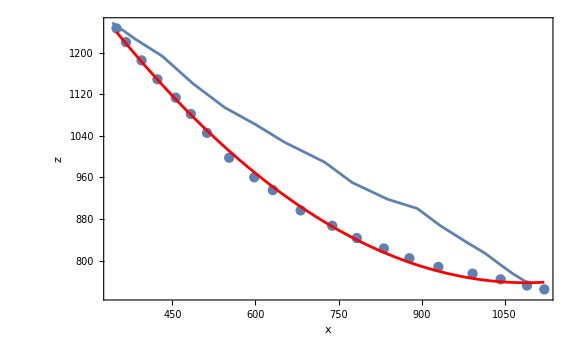

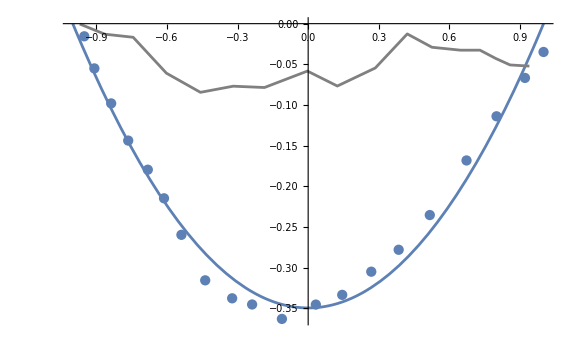

```mathematica
data=Import[NotebookDirectory[]<>"data/LandslideFailureSurfaces.xlsx"];
(*Extract first sheet*)
sheetdata=data[[13]];
(*Take rows 2 to end,first two columns*)
plotDataB=sheetdata[[2;;,1;;2]];  (*rows 2 to end,columns 1 and 2*)
plotDataH=sheetdata[[2;;,3;;4]];  (*rows 2 to end,columns 1 and 2*)
pts = plotDataB;
pts=Select[plotDataB,!AllTrue[#,#===""||#===Null&]&];(*data cleaning*)
(*pts={{x1,z1},{x2,z2},...}*)
xData=pts[[All,1]];
zData=pts[[All,2]];
(*fitResult=IterativeLinearQuadraticVertexFit[pts];
fitResult["VertexParams"]*)

linFit=Fit[Transpose[{xData,zData}],{1,x},x];
α=Abs[Coefficient[linFit,x,1] ](*linear term*)

residuals=zData-(linFit/. x->xData);
quadFit=Fit[Transpose[{xData,residuals}],{1,x,x^2},x];
a=Coefficient[quadFit,x,0];  (*constant term*)
b=Coefficient[quadFit,x,1];  (*linear term*)
c=Coefficient[quadFit,x,2];  (*quadratic term*)
(*convert to form we care about*)
x0=-b/(2 c);
δb=quadFit/.x->x0+Max[Abs[xData-x0]];
b0=b^2/(4 c)-a +δb;
Lx=Max[Abs[xData-x0]];(*Sqrt[x0/c];*)
(*{x0,b0,Lx}*)
b0/Lx

p1=ListPlot[{pts},Frame->True,FrameLabel->{"x","z"}];
p2=ListLinePlot[{plotDataH}];
p3=Plot[linFit+quadFit,{x,Min[xData],Max[xData]},PlotStyle->{Red}];
Show[p1,p2,p3,ImageSize->Large,PlotRange->{Min[zData]-10,Max[zData]+10}]

(*plot rescaled quadratic geometry*)
qF=quadFit/.{x->(x+x0)/Lx};
p1=ListPlot[Transpose[{(xData-x0)/Lx,(residuals-δb)/Lx}]];
p2 = Plot[b0/Lx*(x^2-1),{x,-1,1}];

pts=Select[plotDataH,!AllTrue[#,#===""||#===Null&]&];(*data cleaning*)
xData=pts[[All,1]];
residuals=pts[[All,2]]-(linFit/. x->xData);
p3=ListLinePlot[Transpose[{(xData-x0)/Lx,(residuals-δb)/Lx}],PlotStyle->Gray];
Show[p1,p2,p3,PlotRange->All]
```

```mathematica
(*(*Function to do least squares and estimate shape of landslide base*)
IterativeLinearQuadraticVertexFit[pts_,maxIter_:10,tol_:10^-6]:=Module[{xData,zData,linFit,quadFit,residuals,newResiduals,i,change,a,b,c,A,B,C,vertexFit,fullFit},xData=pts[[All,1]];
zData=pts[[All,2]];
(*Initial linear fit*)
linFit=Fit[Transpose[{xData,zData}],{1,x},x];
change=Infinity;
i=0;
While[i<maxIter&&change>tol,i++;
(*Compute residuals*)
residuals=zData-(linFit/. x->xData);
(*Quadratic fit to residuals*)
quadFit=Fit[Transpose[{xData,residuals}],{1,x,x^2},x];
(*Update linear fit on corrected data*)
newResiduals=zData-(quadFit/. x->xData);
linFit=Fit[Transpose[{xData,newResiduals}],{1,x},x];
(*Measure change in fit*)
change=Max[Abs[newResiduals-residuals]];];
(*Extract coefficients of quadratic*)
a=Coefficient[quadFit,x,0];
b=Coefficient[quadFit,x,1];
c=Coefficient[quadFit,x,2];
(*Convert to vertex form A ((x-B)/C)^2-A*)
B=-b/(2 c);
A=b^2/(4 c)-a;
C=Sqrt[A/c];
vertexFit[x_]:=A*((x-B)/C)^2-A;
(*Full fitted function combining linear+vertex-form quadratic*)
fullFit[x_]:=(linFit/. x->x)+vertexFit[x];
<|"LinearFit"->linFit,"QuadFitCoeffs"->{a,b,c},
"VertexFit"->vertexFit,"VertexParams"->{B,A,C},"FullFit"->fullFit|>]*)
```

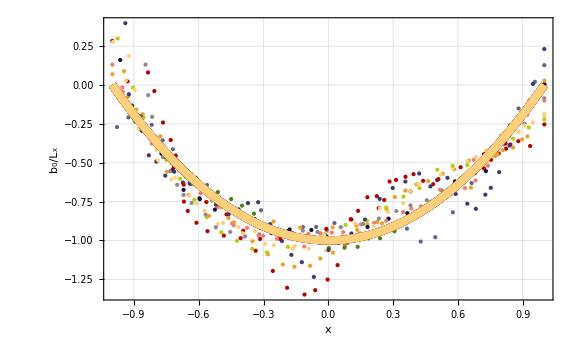

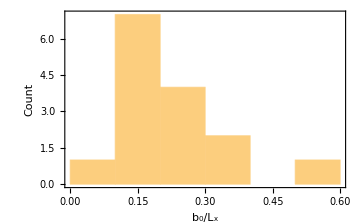

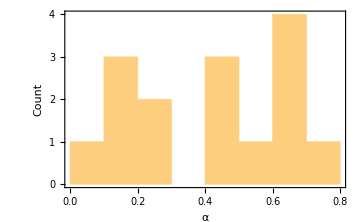

```mathematica
(*Function to process one sheet*)
processSheet[sheet_]:=Module[{pts,xData,zData,linFit,α,residuals,quadFit,a,b,c,x0,Lx,δb,b0,dataRescaled,qF},(*clean data:remove empty rows*)
pts=Select[sheet[[2;;,1;;2]],!AllTrue[#,#===""||#===Null&]&];
xData=pts[[All,1]];
zData=pts[[All,2]];
(*step 1:linear fit*)
linFit=Fit[Transpose[{xData,zData}],{1,x},x];
α=Abs[Coefficient[linFit,x,1] ];(*linear term*)
residuals=zData-(linFit/. x->xData);
(*step 2:quadratic fit to residuals*)
quadFit=Fit[Transpose[{xData,residuals}],{1,x,x^2},x];
a=Coefficient[quadFit,x,0];
b=Coefficient[quadFit,x,1];
c=Coefficient[quadFit,x,2];
(*step 3:rescale to canonical parabola*)x0=-b/(2 c);
Lx=Max[Abs[xData-x0]];
δb=quadFit/. x->(x0+Lx);
b0=b^2/(4 c)-a+δb;
(*rescaled data points*)
(*dataRescaled=Transpose[{(xData-x0)/Lx,(residuals-δb)/Lx}];
(*final parabola in canonical coords*)
qF[x_]:= b0/Lx*(x^2-1);*)
dataRescaled=Transpose[{(xData-x0)/Lx,(residuals-δb)/b0}];
(*final parabola in canonical coords*)
qF[x_]:= 1*(x^2-1);
{dataRescaled,qF,b0/Lx,α}
];

(*Process all 15 sheets*)
processed=processSheet/@data[[1;;15]];

(*Split into data+fits*)
rescaledData=processed[[All,1]];
fits=processed[[All,2]];
b0vals = processed[[All,3]];
αvals = processed[[All,4]];

(*Plot all fitted parabolas together*)
(*Build combined plot*)
Show[Table[
{ListPlot[rescaledData[[i]],PlotStyle->{ColorData[10][i],PointSize[Medium]}],Plot[fits[[i]][x],{x,-1,1},PlotStyle->{ColorData[10][i],Thickness[0.01]}]},
{i,Length[processed]}]//Flatten,
AxesLabel->{Style["x",20],Style[Row[{Subscript["b","0"],"/",Subscript["L","x"]}],20]},FontSize->20,
PlotRange->All,ImageSize->Large,Frame->True,
LabelStyle->Directive[FontSize->20],GridLines->Automatic]
Histogram[b0vals,5,(*number of bins–adjust as you like*)
ChartStyle->Automatic,Frame->True,FrameLabel->{Style[Row[{Subscript["b","0"],"/",Subscript["L","x"]}],20],Style["Count",20]},LabelStyle->Directive[FontSize->15],ImageSize->Medium]
Histogram[αvals,8,(*number of bins–adjust as you like*)
ChartStyle->Automatic,Frame->True,FrameLabel->{Style["α",20],Style["Count",20]},LabelStyle->Directive[FontSize->15],ImageSize->Medium]
```